```mathematica
px[x_,p_]:=Exp[ⅈ*p*x/ℏ];
expx[L_]:=∫_-L^L xⅆx
```

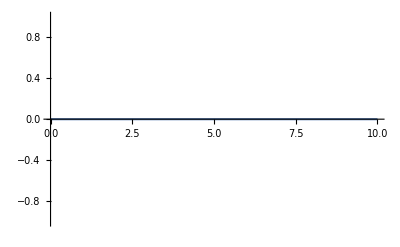

```mathematica
Plot[expx[L],{L,0,10}]
```

```mathematica
∫_(-∞)^∞ xⅆx
```

Integrate::idiv: Integral of x does not converge on {-∞,∞}.

∫_(-∞)^∞ xⅆx

```mathematica
ac[v_,r_]:=v^2/r;
acplus[v_,r_]:=ac[v,r]*1.1;
acminus[v_,r_]:=ac[v,r]*.9;

x0=1;
y0=0;
vx0=0;
vy0=1;
```

```mathematica
ode={x''[t]==-ϵx*x[t]*(x'[t]^2+y'[t]^2)/(x[t]^2+y[t]^2),y''[t]==-ϵy*y[t]*(x'[t]^2+y'[t]^2)/(x[t]^2+y[t]^2),x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0}
```

{x''[t]==-(ϵx x[t] (x'[t]^2+y'[t]^2))/(x[t]^2+y[t]^2),y''[t]==-(ϵy y[t] (x'[t]^2+y'[t]^2))/(x[t]^2+y[t]^2),x[0]==1,y[0]==0,x'[0]==0,y'[0]==1}

{t,0,2 π}

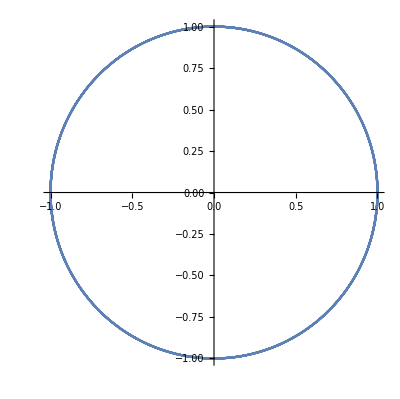

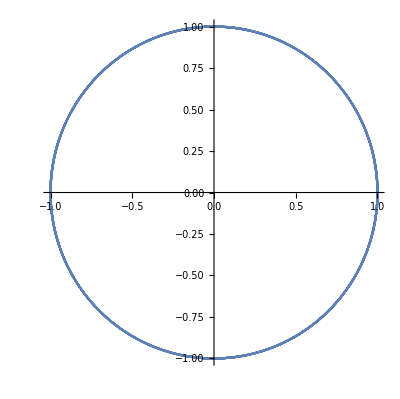

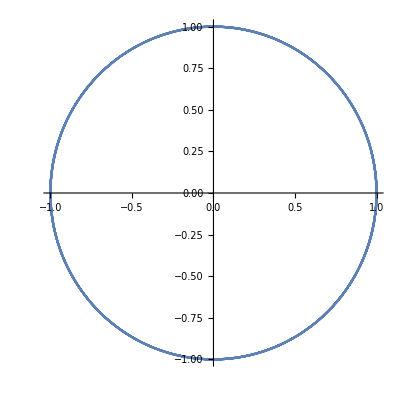

```mathematica
sol=NDSolve[ode/.{ϵx->1,ϵy->1},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.sol,{t,0,8*π}]
ParametricPlot[{x[t],x'[t]}/.sol,{t,0,8*π}]
ParametricPlot[{y[t],y'[t]}/.sol,{t,0,8*π}]
```

```mathematica
solplus=NDSolve[ode/.{ϵx->1.01,ϵy->1.01},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.solplus,{t,0,3.2*π}]
ParametricPlot[{x[t],x'[t]}/.solplus,{t,0,3.2*π}]
ParametricPlot[{y[t],y'[t]}/.solplus,{t,0,3.2*π}]
```

NDSolve::ndsz: At t == 8.85119, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

-Graphics-

-Graphics-

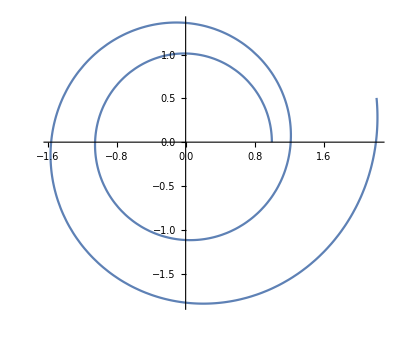

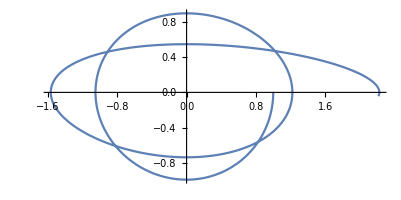

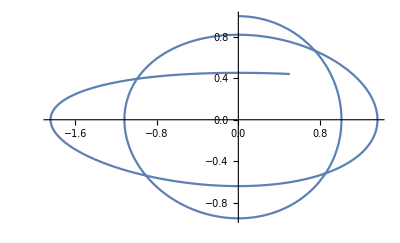

```mathematica
solminus=NDSolve[ode/.{ϵx->0.99,ϵy->0.99},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.solminus,{t,0,8*π}]
ParametricPlot[{x[t],x'[t]}/.solminus,{t,0,8*π}]
ParametricPlot[{y[t],y'[t]}/.solminus,{t,0,8*π}]
```

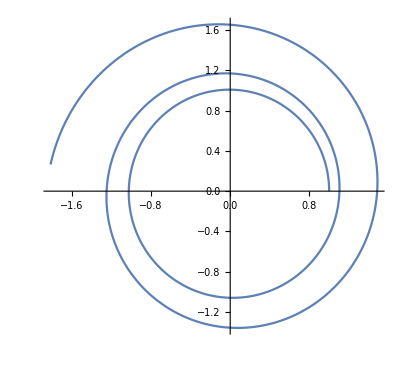

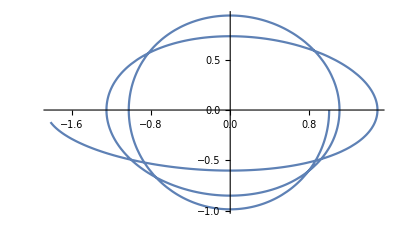

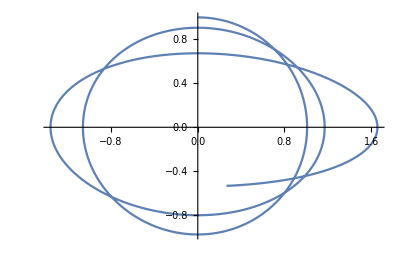

```mathematica
solxm=NDSolve[ode/.{ϵx->0.99,ϵy->1},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.solxm,{t,0,8*π}]
ParametricPlot[{x[t],x'[t]}/.solxm,{t,0,8*π}]
ParametricPlot[{y[t],y'[t]}/.solxm,{t,0,8*π}]
```

NDSolve::ndsz: At t == 12.4708, step size is effectively zero; singularity or stiff system suspected.

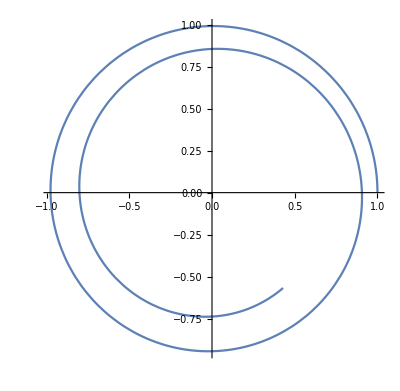

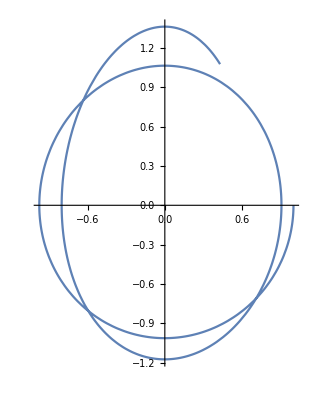

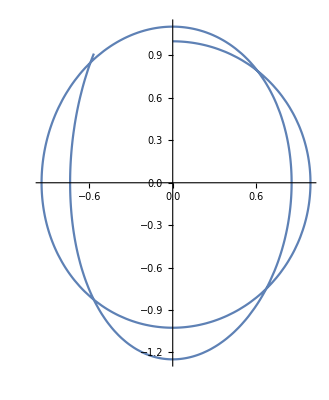

```mathematica
solxp=NDSolve[ode/.{ϵx->1.01,ϵy->1},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.solxp,{t,0,3*π}]
ParametricPlot[{x[t],x'[t]}/.solxp,{t,0,3*π}]
ParametricPlot[{y[t],y'[t]}/.solxp,{t,0,3*π}]
```

NDSolve::ndsz: At t == 15.1495, step size is effectively zero; singularity or stiff system suspected.

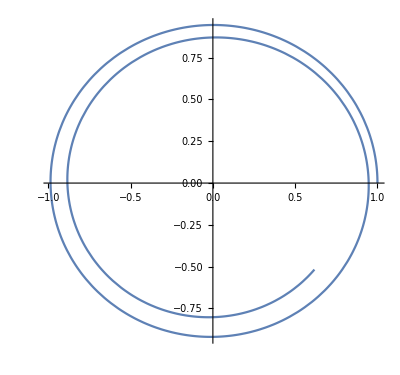

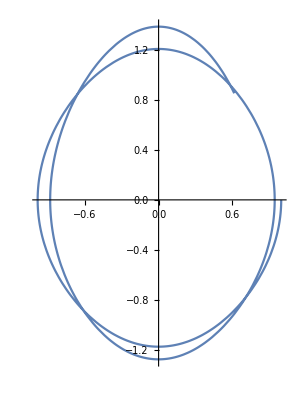

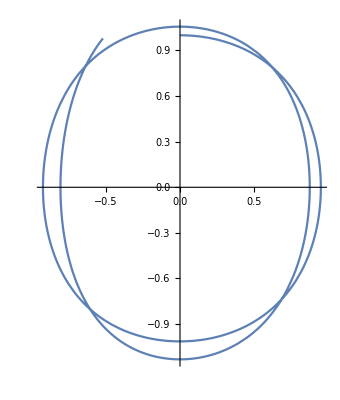

```mathematica
solxpym=NDSolve[ode/.{ϵx->1/0.9,ϵy->0.9},{x,y},{t,0,8*π}];
ParametricPlot[{x[t],y[t]}/.solxpym,{t,0,3*π}]
ParametricPlot[{x[t],x'[t]}/.solxpym,{t,0,3*π}]
ParametricPlot[{y[t],y'[t]}/.solxpym,{t,0,3*π}]
```

```mathematica
"xp and ym can give infalling or outgoing solns depending on which is gibber or smaller"
```

xp and ym can give infalling or outgoing solns depending on which is gibber or smaller

0 deg phase shift, cos +

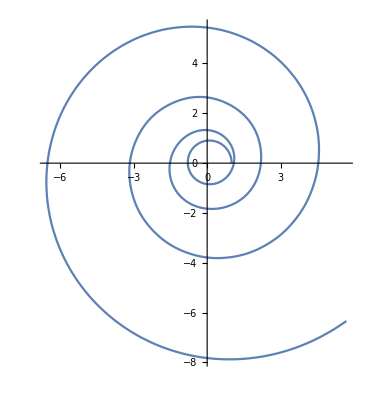

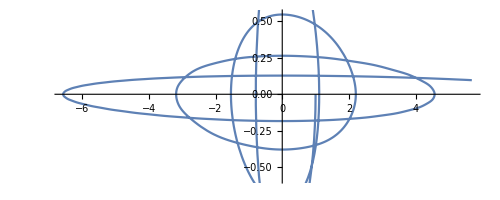

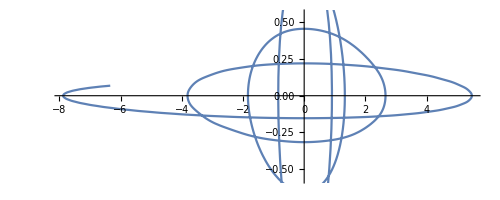

```mathematica
"0 deg phase shift, cos +"
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1+.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

0 deg phase shift, cos -

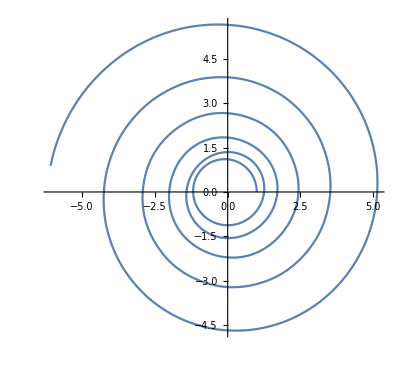

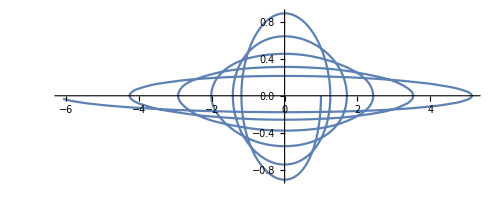

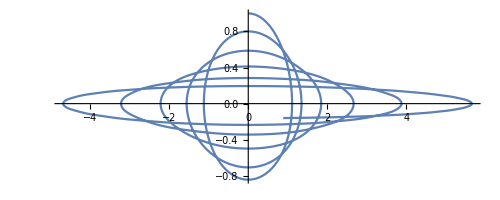

```mathematica
"0 deg phase shift, cos -"
solosc=NDSolve[ode/.{ϵx->1-.1*Cos[t],ϵy->1-.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

0 deg phase shift, sin +

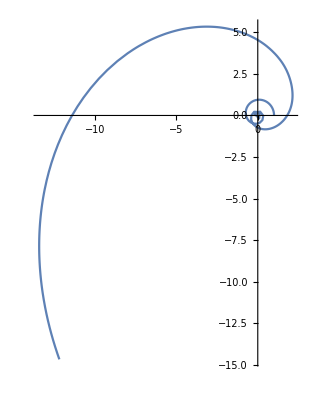

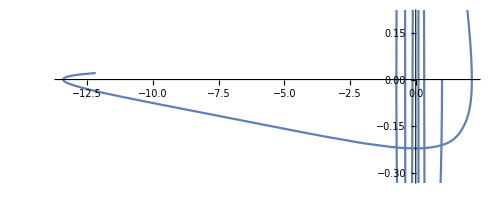

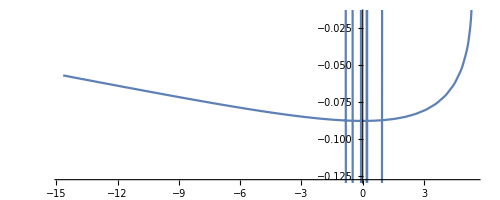

```mathematica
"0 deg phase shift, sin +"
solosc=NDSolve[ode/.{ϵx->1+.1*Sin[t],ϵy->1+.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

0 deg phase shift, sin -

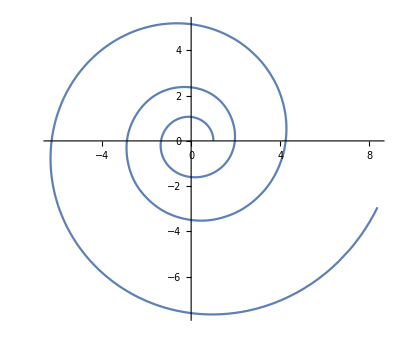

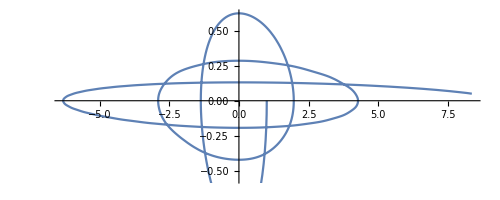

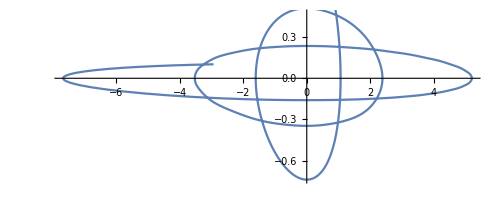

```mathematica
"0 deg phase shift, sin -"
solosc=NDSolve[ode/.{ϵx->1-.1*Sin[t],ϵy->1-.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

90 deg phase shift, cos +

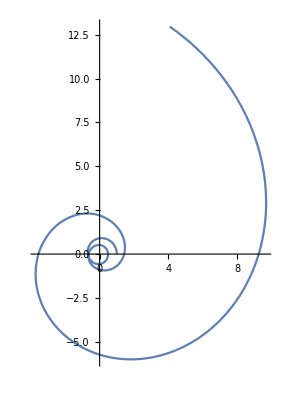

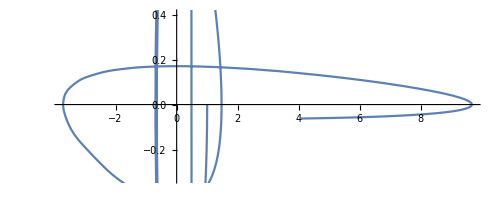

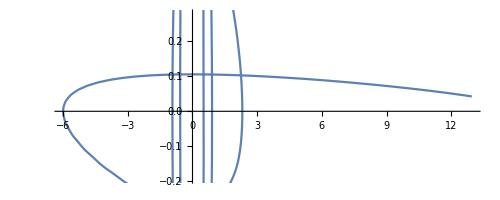

```mathematica
"90 deg phase shift, cos +"
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1+.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

90 deg phase shift, cos -

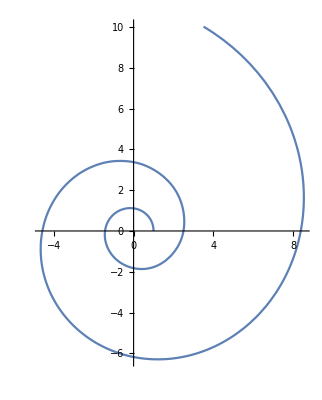

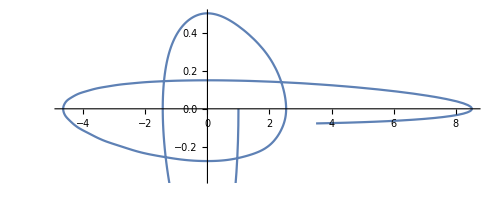

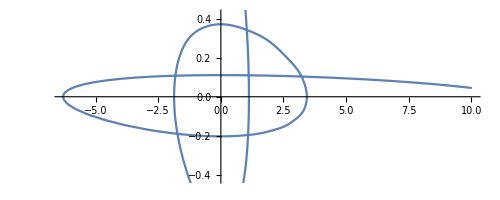

```mathematica
"90 deg phase shift, cos -"
solosc=NDSolve[ode/.{ϵx->1-.1*Cos[t],ϵy->1-.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

90 deg phase shift, sin +

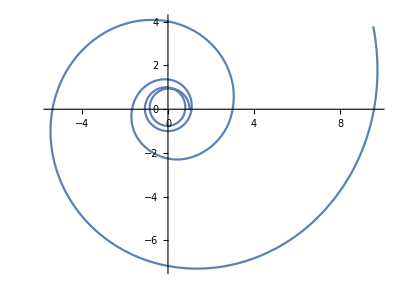

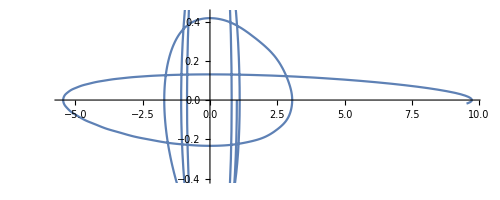

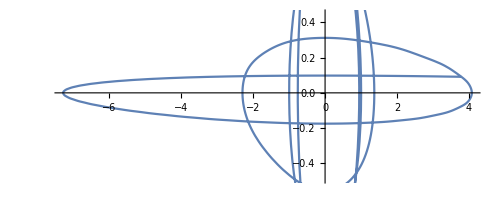

```mathematica
"90 deg phase shift, sin +"
solosc=NDSolve[ode/.{ϵx->1+.1*Sin[t],ϵy->1+.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

90 deg phase shift, sin -

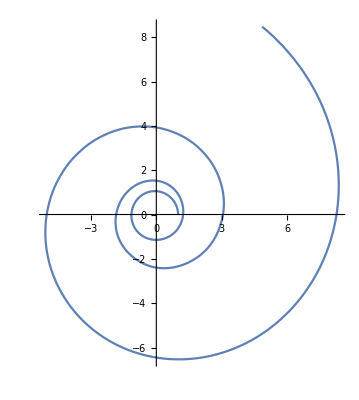

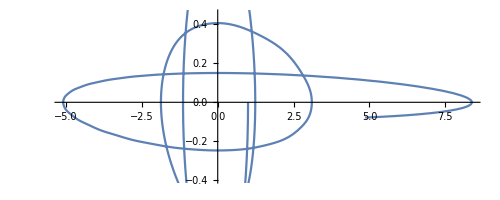

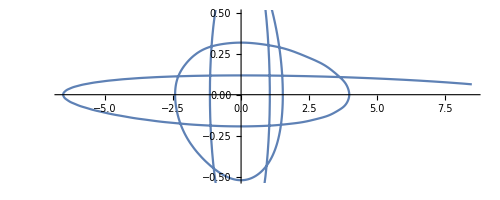

```mathematica
"90 deg phase shift, sin -"
solosc=NDSolve[ode/.{ϵx->1-.1*Sin[t],ϵy->1+-.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

180 deg phase shift, cos +

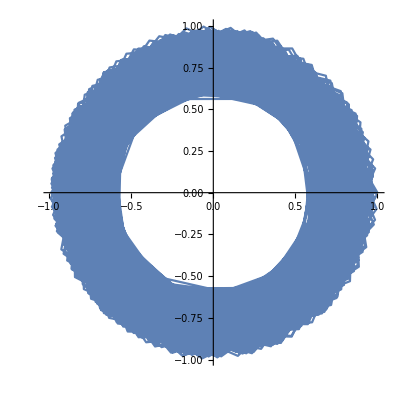

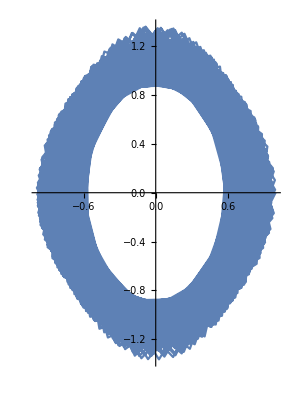

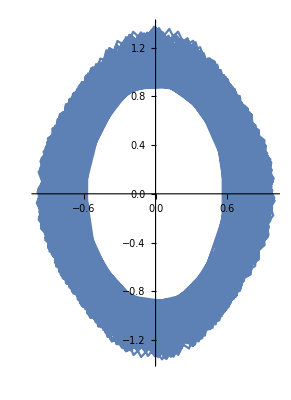

```mathematica
"180 deg phase shift, cos +"
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1-.1*Cos[t]},{x,y},{t,0,1000*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,1000*π}]
```

```mathematica
"dense orbits!"
```

dense orbits!

180 deg phase shift, cos -

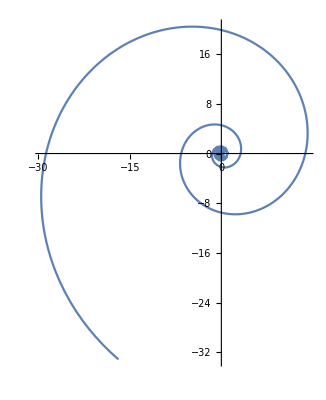

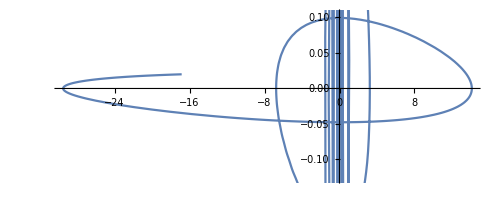

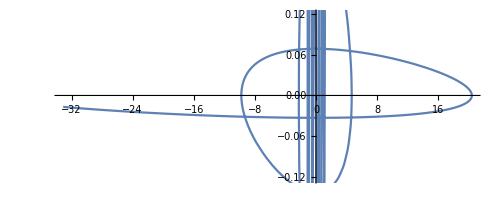

```mathematica
"180 deg phase shift, cos -"
solosc=NDSolve[ode/.{ϵx->1-.1*Cos[t],ϵy->1+.1*Cos[t]},{x,y},{t,0,1000*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,1000*π}]
```

180 deg phase shift, sin +

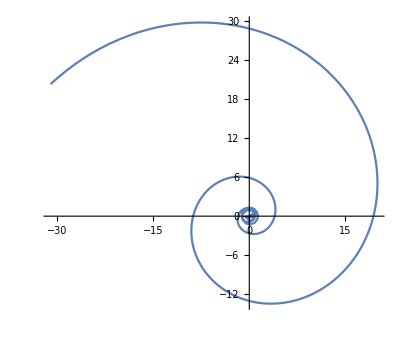

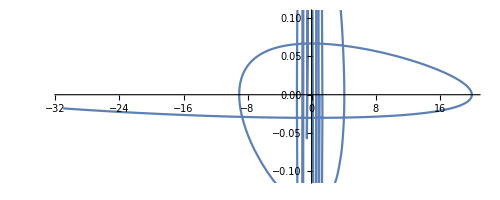

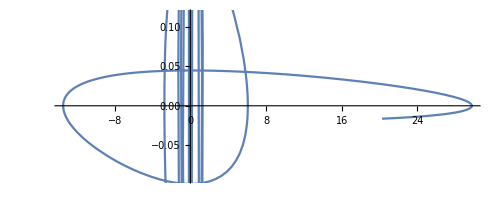

```mathematica
"180 deg phase shift, sin +"
solosc=NDSolve[ode/.{ϵx->1+.1*Sin[t],ϵy->1-.1*Sin[t]},{x,y},{t,0,1000*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,1000*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,1000*π}]
```

180 deg phase shift, sin -

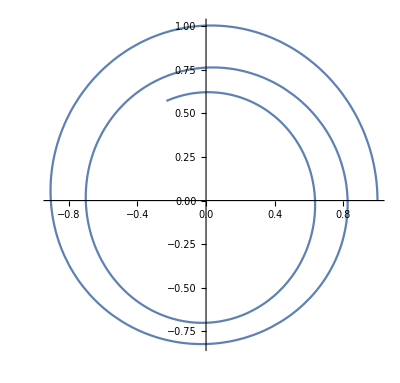

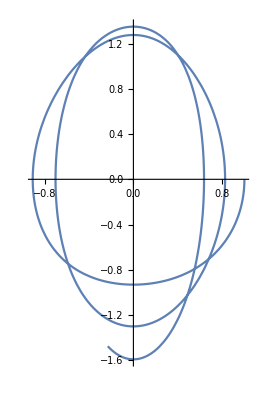

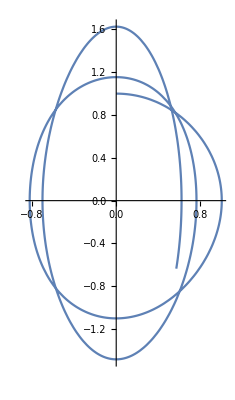

```mathematica
"180 deg phase shift, sin -"
solosc=NDSolve[ode/.{ϵx->1-.1*Sin[t],ϵy->1+.1*Sin[t]},{x,y},{t,0,3*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,3*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,3*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,3*π}]
```

```mathematica
"spirals in!"
```

spirals in!

270 deg phase shift, cos +

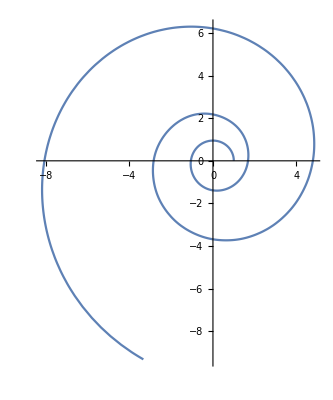

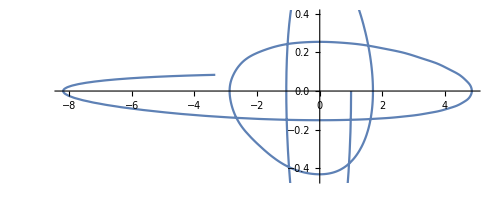

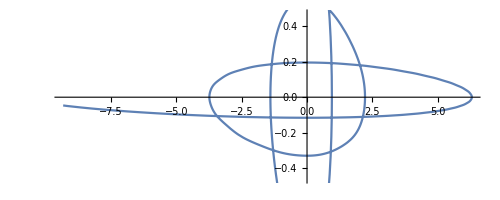

```mathematica
"270 deg phase shift, cos +"
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1-.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

270 deg phase shift, cos -

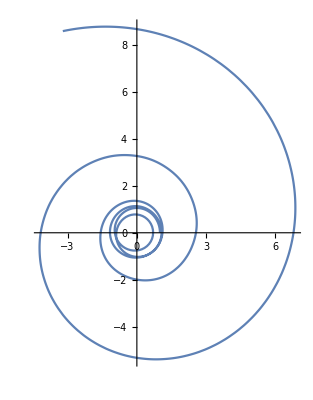

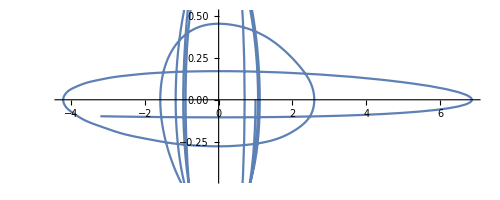

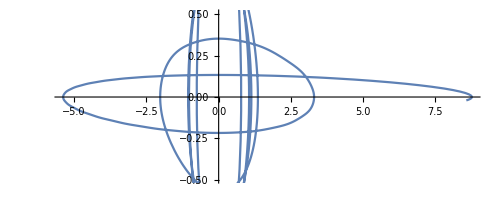

```mathematica
"270 deg phase shift, cos -"
solosc=NDSolve[ode/.{ϵx->1-.1*Cos[t],ϵy->1+.1*Sin[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

270 deg phase shift, sin +

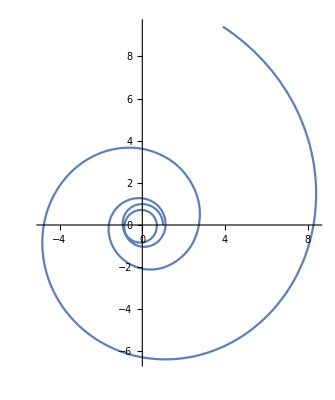

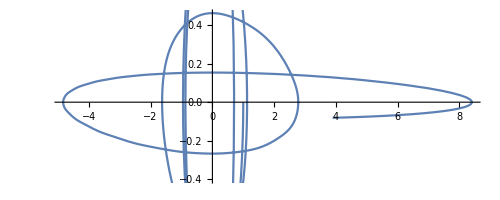

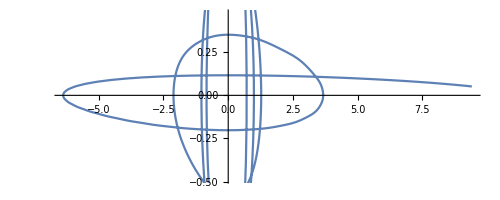

```mathematica
"270 deg phase shift, sin +"
solosc=NDSolve[ode/.{ϵx->1+.1*Sin[t],ϵy->1-.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

270 deg phase shift, sin -

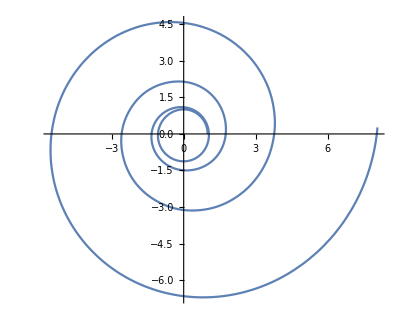

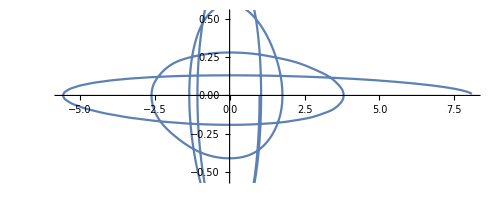

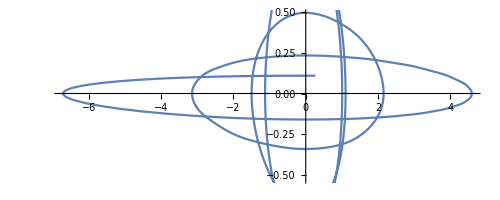

```mathematica
"270 deg phase shift, sin -"
solosc=NDSolve[ode/.{ϵx->1-.1*Sin[t],ϵy->1+.1*Cos[t]},{x,y},{t,0,100*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,100*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,100*π}]
```

```mathematica
"Explore more of 180deg cos+ and sin- orbit and inspiral"
```

Explore more of 180deg cos+ and sin- orbit and inspiral

180 deg phase shift, cos +

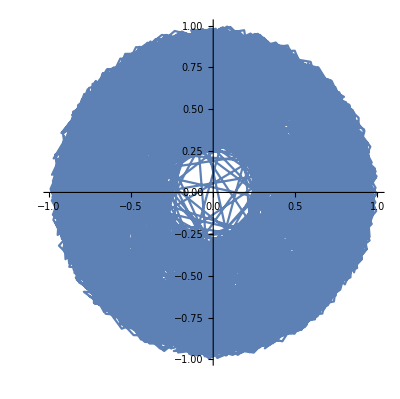

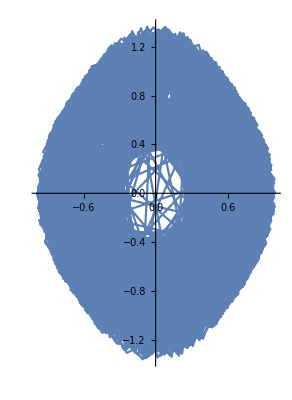

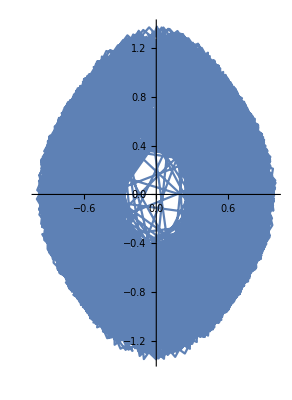

```mathematica
"180 deg phase shift, cos +"
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1-.1*Cos[t]},{x,y},{t,0,10000*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,10000*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,10000*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,10000*π}]
```

180 deg phase shift, cos +

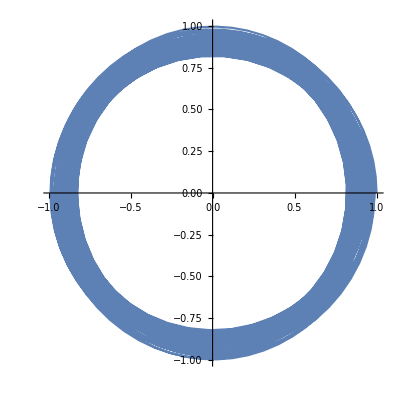

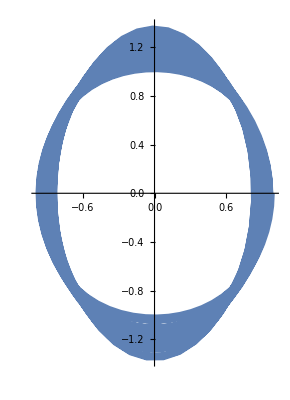

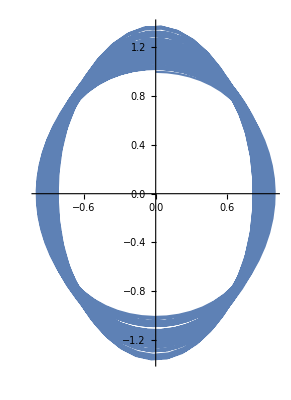

```mathematica
"180 deg phase shift, cos +"
tmax=100;
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[t],ϵy->1-.1*Cos[t]},{x,y},{t,0,tmax*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,tmax*π}]
```

```mathematica
"now try different harmonics"
```

now try different harmonics

```mathematica
"180 deg phase shift, cos +"
tmax=2;
ω=2.00;
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[ω*t],ϵy->1-.1*Cos[ω*t]},{x,y},{t,0,tmax*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,tmax*π}]
```

180 deg phase shift, cos +

NDSolve::ndsz: At t == 5.50426, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

-Graphics-

-Graphics-

```mathematica
"ω->2 system inspirals"
```

ω->2 system inspirals

180 deg phase shift, cos +

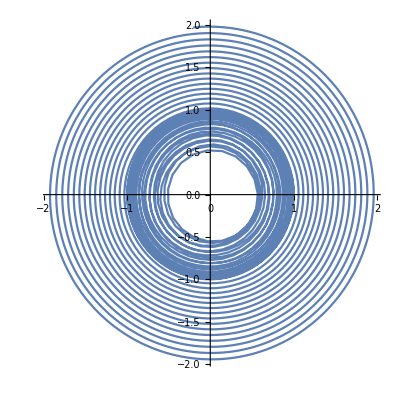

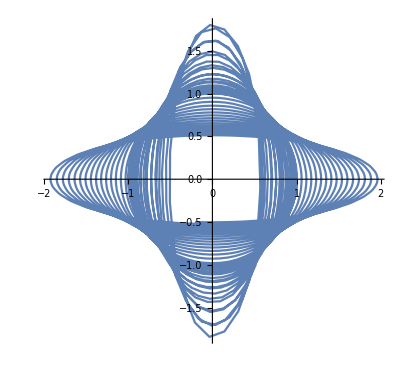

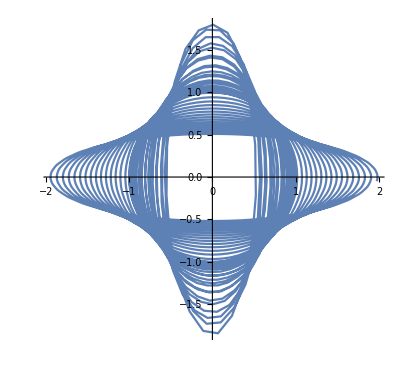

```mathematica
"180 deg phase shift, cos +"
tmax=100;
ω=10;
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[ω*t],ϵy->1-.1*Cos[ω*t]},{x,y},{t,0,tmax*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,tmax*π}]
```

```mathematica
"integer multiples of ω=/=2 seem to give more closer appraoch to origin, but end actually outside, so they never fall in"
```

integer multiples of ω=/=2 seem to give more closer appraoch to origin, but end actually outside, so they never fall in

180 deg phase shift, cos +

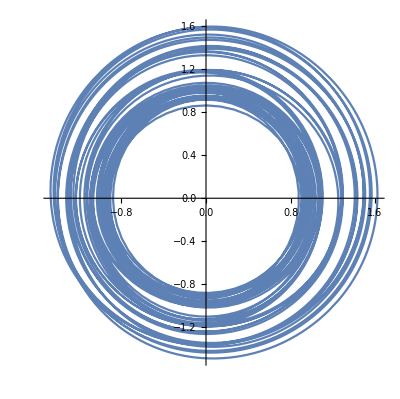

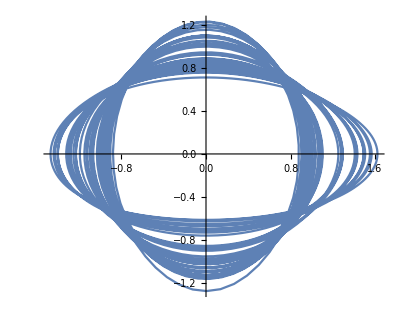

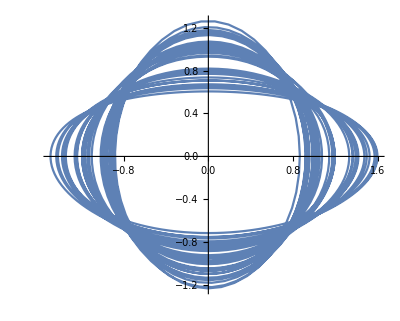

```mathematica
"180 deg phase shift, cos +"
tmax=100;
ω=.5;
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[ω*t],ϵy->1-.1*Cos[ω*t]},{x,y},{t,0,tmax*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,tmax*π}]
```

180 deg phase shift, cos +

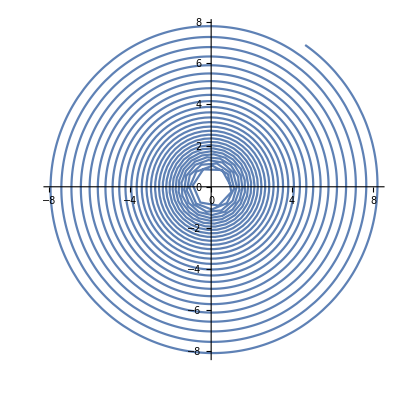

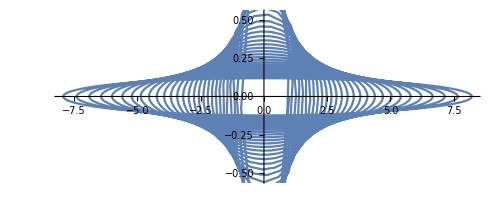

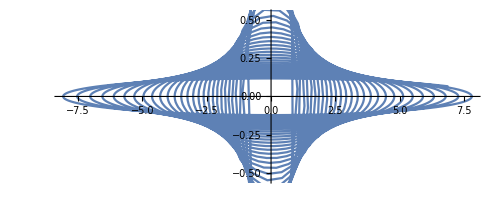

```mathematica
"180 deg phase shift, cos +"
tmax=1000;
ω=π;
solosc=NDSolve[ode/.{ϵx->1+.1*Cos[ω*t],ϵy->1-.1*Cos[ω*t]},{x,y},{t,0,tmax*π}];
ParametricPlot[{x[t],y[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{x[t],x'[t]}/.solosc,{t,0,tmax*π}]
ParametricPlot[{y[t],y'[t]}/.solosc,{t,0,tmax*π}]
```